## Мухамадиев Владимир

# Задание 8

## Загрузка и предварительная обработка

```mathematica
g1=ConnectedGraphComponents[SimpleGraph[UndirectedGraph[Import[FileNameJoin[{NotebookDirectory[],"cat.graphml"}]]]]]⟦1⟧;
```

```mathematica
g2=ConnectedGraphComponents[SimpleGraph[UndirectedGraph[Import[FileNameJoin[{NotebookDirectory[],"c-elegans.graphml"}]]]]]⟦1⟧;
```

```mathematica
g3=ConnectedGraphComponents[SimpleGraph[UndirectedGraph[Import[FileNameJoin[{NotebookDirectory[],"drosophila.graphml"}]]]]]⟦1⟧;
```

```mathematica
g4=ConnectedGraphComponents[SimpleGraph[UndirectedGraph[Import[FileNameJoin[{NotebookDirectory[],"macaque.graphml"}]]]]]⟦1⟧;
```

```mathematica
g5=ConnectedGraphComponents[SimpleGraph[UndirectedGraph[Import[FileNameJoin[{NotebookDirectory[],"mouse.graphml"}]]]]]⟦1⟧;
```

```mathematica
g6=ConnectedGraphComponents[SimpleGraph[UndirectedGraph[Import[FileNameJoin[{NotebookDirectory[],"rat.graphml"}]]]]]⟦1⟧;
```

```mathematica
sre=Import[FileNameJoin[{NotebookDirectory[],"sre.m"}]];
```

```mathematica
re=Import[FileNameJoin[{NotebookDirectory[],"re.m"}]];
```

## 1. Random walk normalized Laplacian

```mathematica
RWNL[graph_]:=Inverse[DiagonalMatrix[VertexDegree[graph]]].KirchhoffMatrix[graph]
```

```mathematica
HPDF[graph_,r_]:=Module[{ei=Eigenvalues[N[RWNL[graph]]]},{Range[0,2,1/VertexCount[graph]],Flatten[Append[MovingAverage[Table[Evaluate[PDF[HistogramDistribution[ei,VertexCount[graph]],i]],{i,0,2,1/VertexCount[graph]}],r],ConstantArray[0,r-1]]]}ᵀ]
```

```mathematica
g1d=HPDF[g1,Round[VertexCount[g1]/10]];
```

```mathematica
g2d=HPDF[g2,Round[VertexCount[g2]/10]];
```

```mathematica
g3d=HPDF[g3,Round[VertexCount[g3]/10]];
```

```mathematica
g4d=HPDF[g4,Round[VertexCount[g4]/10]];
```

```mathematica
g5d=HPDF[g5,Round[VertexCount[g5]/10]];
```

```mathematica
g6d=HPDF[g6,Round[VertexCount[g6]/10]];
```

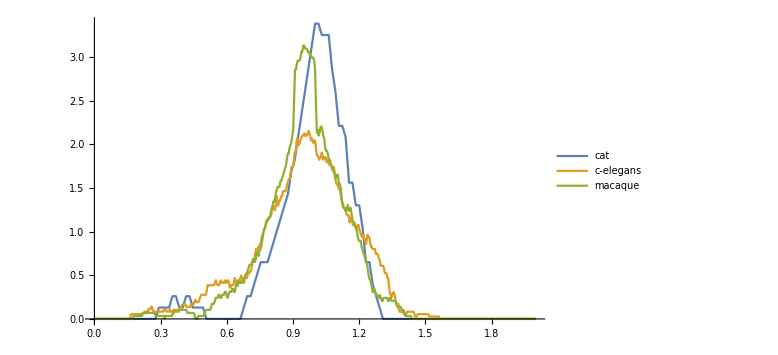

```mathematica
ListLinePlot[{g1d,g2d,g4d},PlotRange->All,PlotLegends->Placed[{"cat","c-elegans","macaque"},Below],ImageSize->Large]
```

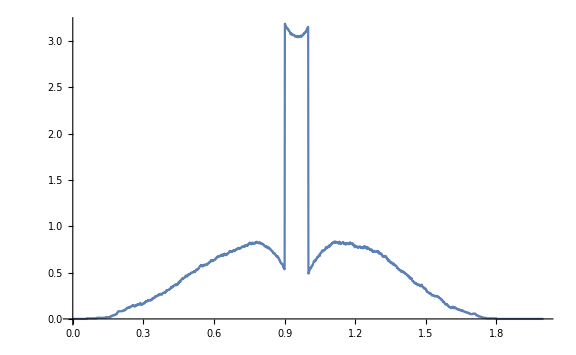

```mathematica
ListLinePlot[g3d,PlotRange->All,PlotLegends->Placed["drosophila",Below],ImageSize->Large]
```

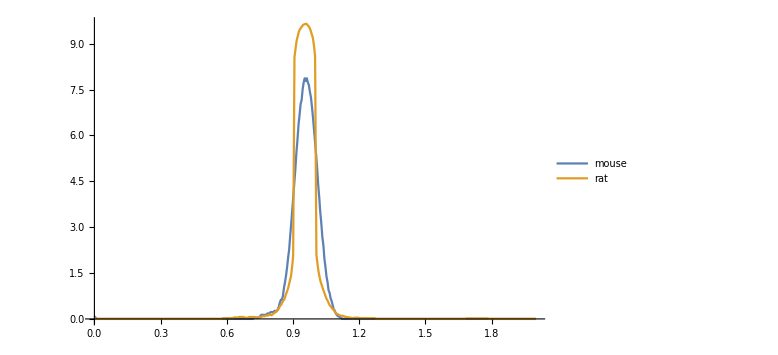

```mathematica
ListLinePlot[{g5d,g6d},PlotRange->All,PlotLegends->Placed[{"mouse","rat"},Below],ImageSize->Large]
```

## 2. Устойчивость коннектомов

### Функция которая приводит список ребер к виду, где в каждом ребре v_1<->v_2,v_1≤v_2

```mathematica
EdgeSort[edgelist_]:=Module[{out=edgelist},Do[If[edgelist⟦i,1⟧>edgelist⟦i,2⟧,out⟦i⟧=edgelist⟦i,2⟧<->edgelist⟦i,1⟧],{i,1,Length[edgelist]}];out]
```

### Рандомизация графа без сохранения степеней вершин

```mathematica
GraphSimpleRandomization[graph_,n_]:=Module[{el=EdgeSort[EdgeList[graph]],vl=VertexList[graph],temp={}},Do[temp=RandomChoice[el];While[VertexDegree[graph,temp⟦1⟧]==1||VertexDegree[graph,temp⟦2⟧]==1,temp=RandomChoice[el]];el=DeleteCases[el,temp];temp=RandomSample[vl,2];temp=EdgeSort[{temp⟦1⟧<->temp⟦2⟧}]⟦1⟧;While[ContainsAll[el,{temp}]==True,temp=RandomSample[vl,2];temp=EdgeSort[{temp⟦1⟧<->temp⟦2⟧}]⟦1⟧];AppendTo[el,temp],{i,1,n}];Graph[el]]
```

### Рандомизация графа с сохранением степеней вершин

```mathematica
GraphRandomization[g_,n_]:=Module[{el=EdgeSort[EdgeList[g]],eltemp={},vltemp={},temp={{},{}},k=0},Do[temp⟦1⟧=RandomChoice[el](*Выбираем первое ребро/петлю*);eltemp=DeleteCases[el,temp⟦1⟧](*Создаем временную выборку из ребер/петель и удалаем из нее все мультиребра/мультипетли для выбранного ребра/петли*);If[temp⟦1,1⟧==temp⟦1,2⟧,(*Алгоритм выбрал петлю*)eltemp=DeleteCases[eltemp,v_<->v_](*удаляем из временной выбрки все петли*);vltemp=Flatten[{Cases[eltemp,temp⟦1,1⟧<->_],Cases[eltemp,_<->temp⟦1,1⟧]}];vltemp=DeleteDuplicates[Flatten[{vltemp⟦All,1⟧,vltemp⟦All,2⟧}]](*Список вершин с которыми граничит выбранная петля*);Do[eltemp=DeleteCases[eltemp,vltemp⟦j⟧<->_];eltemp=DeleteCases[eltemp,_<->vltemp⟦j⟧],{j,1,Length[vltemp]}](*Удаляем из временной выборки все ребра/петли, вершины которых связаны с данной петлей*);If[eltemp=={},i++;Goto[end](*Алгоритм выбрал петлю которую нельзя изменить, так как до любой вершины из нее можно добраться в два шага. Переходим в конец цикла и считаем что на этом шаге ничего не поменялось*),temp⟦2⟧=RandomChoice[eltemp](*Выбираем второе ребро*)],(*Алгоритм выбрал ребро*)vltemp=Flatten[{Cases[eltemp,temp⟦1,1⟧<->_],Cases[eltemp,_<->temp⟦1,1⟧],Cases[eltemp,temp⟦1,2⟧<->_],Cases[eltemp,_<->temp⟦1,2⟧]}];vltemp=DeleteDuplicates[Flatten[{vltemp⟦All,1⟧,vltemp⟦All,2⟧}]](*Список вершин с которыми граничит выбранное ребро*);Do[eltemp=DeleteCases[eltemp,vltemp⟦j⟧<->_];eltemp=DeleteCases[eltemp,_<->vltemp⟦j⟧],{j,1,Length[vltemp]}](*Удаляем из временной выборки все ребра/петли, вершины которых связаны с данным ребром*);If[eltemp=={},i++;Goto[end](*Алгоритм выбрал ребро которое нельзя изменить, так как до любой вершины из него можно добраться в два шага. Переходим в конец цикла и считаем что на этом шаге ничего не поменялось*),temp⟦2⟧=RandomChoice[eltemp](*Выбираем второе ребро/петлю*)]];k=1;While[(el⟦k⟧===temp⟦1⟧)==False,k++];el=Delete[el,k];k=1;While[(el⟦k⟧===temp⟦2⟧)==False,k++];el=Delete[el,k](*Удаляем из списка ребер выбранные*);If[RandomInteger[{1,2}]==1(*Случайно выбираем как переключить ребра и добавляем новые к списку ребер*),AppendTo[el,EdgeSort[{temp⟦1,1⟧<->temp⟦2,1⟧}]⟦1⟧];AppendTo[el,EdgeSort[{temp⟦1,2⟧<->temp⟦2,2⟧}]⟦1⟧],AppendTo[el,EdgeSort[{temp⟦1,1⟧<->temp⟦2,2⟧}]⟦1⟧];AppendTo[el,EdgeSort[{temp⟦1,2⟧<->temp⟦2,1⟧}]⟦1⟧]];Label[end],{i,1,n}];Graph[el]]
```

### Эволюция расстояния между спектрами графа и графа после рандомизации

#### Без сохранения степеней вершин

```mathematica
SRE[graph_,t_,Δt_]:=Module[{temp=graph,ei0=Eigenvalues[N[RWNL[graph]]],out=ConstantArray[{0,0},Round[t/Δt]+1]},Do[temp=GraphSimpleRandomization[temp,Round[Δt]];out⟦i+1⟧={i Round[Δt],EuclideanDistance[ei0,Eigenvalues[N[RWNL[temp]]]]},{i,1,Round[t/Δt]}];out]
```

```mathematica
g1sre=sre⟦1⟧;
(*g1sre=SRE[g1,2EdgeCount[g1],EdgeCount[g1]/100 ]ᵀ;
g1sre⟦1⟧=N[g1sre⟦1⟧/EdgeCount[g1]];
g1sre=g1sreᵀ;*)
```

```mathematica
g2sre=sre⟦2⟧;
(*g2sre=SRE[g2,2EdgeCount[g2],EdgeCount[g2]/100 ]ᵀ;
g2sre⟦1⟧=N[g2sre⟦1⟧/EdgeCount[g2]];
g2sre=g2sreᵀ;*)
```

```mathematica
g3sre=sre⟦3⟧;
(*g3sre=SRE[g3,2EdgeCount[g3],EdgeCount[g3]/100 ]ᵀ;
g3sre⟦1⟧=N[g3sre⟦1⟧/EdgeCount[g3]];
g3sre=g3sreᵀ;*)
```

```mathematica
g4sre=sre⟦4⟧;
(*g4sre=SRE[g4,2EdgeCount[g4],EdgeCount[g4]/100 ]ᵀ;
g4sre⟦1⟧=N[g4sre⟦1⟧/EdgeCount[g4]];
g4sre=g4sreᵀ;*)
```

```mathematica
g5sre=sre⟦5⟧;
(*g5sre=SRE[g5,2EdgeCount[g5],EdgeCount[g5]/100 ]ᵀ;
g5sre⟦1⟧=N[g5sre⟦1⟧/EdgeCount[g5]];
g5sre=g5sreᵀ;*)
```

```mathematica
g6sre=sre⟦6⟧;
(*g6sre=SRE[g6,2EdgeCount[g6],EdgeCount[g6]/100 ]ᵀ;
g6sre⟦1⟧=N[g6sre⟦1⟧/EdgeCount[g6]];
g6sre=g6sreᵀ;*)
```

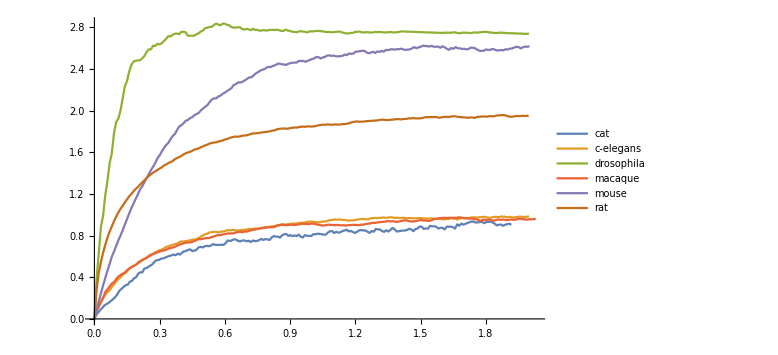

```mathematica
ListLinePlot[{g1sre,g2sre,g3sre,g4sre,g5sre,g6sre},PlotLegends->Placed[{"cat","c-elegans","drosophila","macaque","mouse","rat"},Below],ImageSize->Large]
```

#### С сохранением степеней вершин

```mathematica
RE[graph_,t_,Δt_]:=Module[{temp=graph,ei0=Eigenvalues[N[RWNL[graph]]],out=ConstantArray[{0,0},Round[t/Δt]+1]},Do[temp=GraphRandomization[temp,Round[Δt]];out⟦i+1⟧={i Round[Δt],EuclideanDistance[ei0,Eigenvalues[N[RWNL[temp]]]]},{i,1,Round[t/Δt]}];out]
```

```mathematica
g1re=re⟦1⟧;
(*g1re=RE[g1,2EdgeCount[g1],EdgeCount[g1]/100 ]ᵀ;
g1re⟦1⟧=N[g1re⟦1⟧/EdgeCount[g1]];
g1re=g1reᵀ;*)
```

```mathematica
g2re=re⟦2⟧;
(*g2re=RE[g2,2EdgeCount[g2],EdgeCount[g2]/100 ]ᵀ;
g2re⟦1⟧=N[g2re⟦1⟧/EdgeCount[g2]];
g2re=g2reᵀ;*)
```

```mathematica
g3re=re⟦3⟧;
(*g3re=RE[g3,2EdgeCount[g3],EdgeCount[g3]/100 ]ᵀ;
g3re⟦1⟧=N[g3re⟦1⟧/EdgeCount[g3]];
g3re=g3reᵀ;*)
```

```mathematica
g4re=re⟦4⟧;
(*g4re=RE[g4,2EdgeCount[g4],EdgeCount[g4]/100 ]ᵀ;
g4re⟦1⟧=N[g4re⟦1⟧/EdgeCount[g4]];
g4re=g4reᵀ;*)
```

```mathematica
g5re=re⟦5⟧;
(*g5re=RE[g5,2EdgeCount[g5],EdgeCount[g5]/100 ]ᵀ;
g5re⟦1⟧=N[g5re⟦1⟧/EdgeCount[g5]];
g5re=g5reᵀ;*)
```

```mathematica
g6re=re⟦6⟧;
(*g6re=RE[g6,2EdgeCount[g6],EdgeCount[g6]/100 ]ᵀ;
g6re⟦1⟧=N[g6re⟦1⟧/EdgeCount[g6]];
g6re=g6reᵀ;*)
```

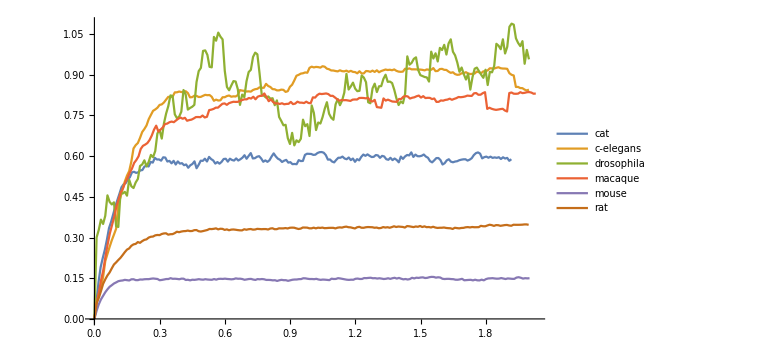

```mathematica
ListLinePlot[{g1re,g2re,g3re,g4re,g5re,g6re},PlotLegends->Placed[{"cat","c-elegans","drosophila","macaque","mouse","rat"},Below],ImageSize->Large]
```

## 3. Схожесть спектров различных организмов

### Распределение по гистограмме собственных значений RWNL

```mathematica
RWNLHD[graph_,Δ_]:=Table[Evaluate[PDF[HistogramDistribution[Eigenvalues[N[RWNL[graph]]],VertexCount[graph]],i]],{i,0,2,Δ}]
```

```mathematica
dist={RWNLHD[g1,0.001],RWNLHD[g2,0.001],RWNLHD[g3,0.001],RWNLHD[g4,0.001],RWNLHD[g5,0.001],RWNLHD[g6,0.001]};
```

### Граф расстояний между распределениями

#### Евклидово расстояние

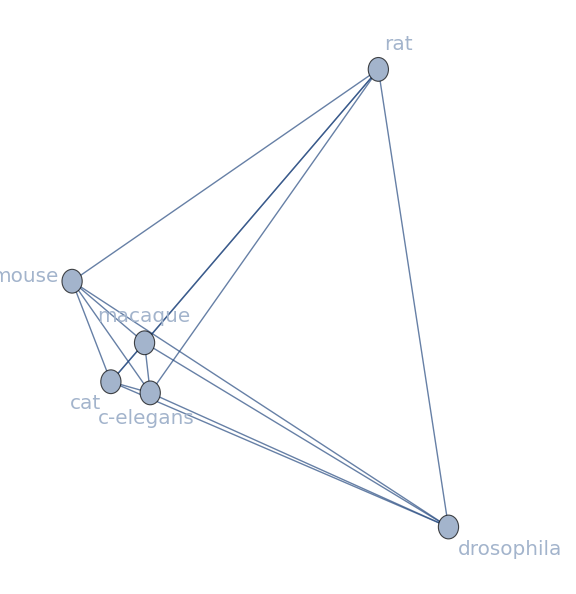

```mathematica
CompleteGraph[6,EdgeWeight->Flatten[Table[EuclideanDistance[dist⟦i⟧,dist⟦j⟧],{i,1,5},{j,i+1,6}]],GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}},VertexLabels->{1->Style["cat",20],2->Style["c-elegans",20],3->Style["drosophila",20],4->Style["macaque",20],5->Style["mouse",20],6->Style["rat",20]},VertexSize->0.5,ImageSize->Large]
```

#### Расстояние Чебышева

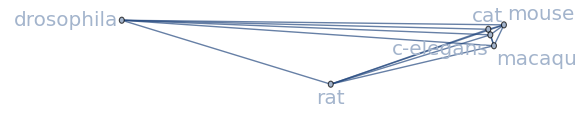

```mathematica
CompleteGraph[6,EdgeWeight->Flatten[Table[ChessboardDistance[dist⟦i⟧,dist⟦j⟧],{i,1,5},{j,i+1,6}]],GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}},VertexLabels->{1->Style["cat",20],2->Style["c-elegans",20],3->Style["drosophila",20],4->Style["macaque",20],5->Style["mouse",20],6->Style["rat",20]},VertexSize->1,ImageSize->Large]
```

#### Манхэттенское расстояние

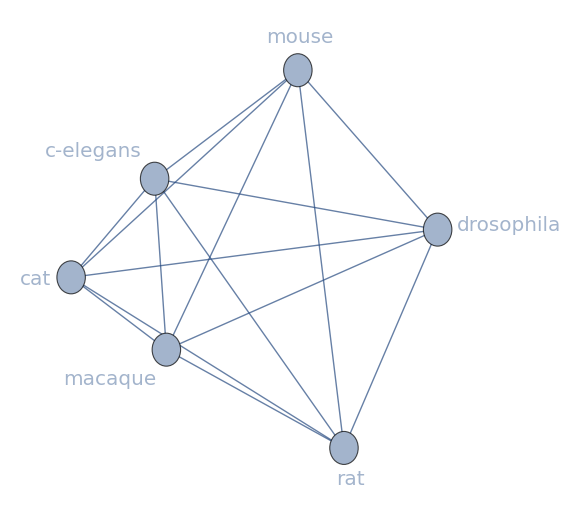

```mathematica
CompleteGraph[6,EdgeWeight->Flatten[Table[ManhattanDistance[dist⟦i⟧,dist⟦j⟧],{i,1,5},{j,i+1,6}]],GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}},VertexLabels->{1->Style["cat",20],2->Style["c-elegans",20],3->Style["drosophila",20],4->Style["macaque",20],5->Style["mouse",20],6->Style["rat",20]},VertexSize->0.25,ImageSize->Large]
```